```mathematica
I1=Import["iguales1.dat","Data"]
```

{{0.,1.},{0.001,1.005},{0.002,1.01},{0.003,1.015},{0.004,1.02},{0.005,1.025},«2892»,{2.897,4.535},{2.898,4.53},{2.899,4.525},{2.9,4.52},{2.901,4.515},{2.902,4.51}}

```mathematica
I2=Import["iguales2.dat","Data"]
```

{{0.,9.},{0.001,8.995},{0.002,8.99},{0.003,8.985},{0.004,8.98},{0.005,8.975},«2893»,{2.898,5.49},{2.899,5.495},{2.9,5.5},{2.901,5.505},{2.902,5.51}}

```mathematica
V1=Import["varios1.dat","Data"]
```

{{0.,1.},{0.001,1.01},{0.002,1.02},{0.003,1.03},{0.004,1.04},{0.005,1.05},«3295»,{3.267,5.56},{3.268,5.55},{3.269,5.54},{3.27,5.53},{3.271,5.52},{3.272,5.51}}

```mathematica
V2=Import["varios2.dat", "Data"]
```

{{0.,9.},{0.001,8.995},{0.002,8.99},{0.003,8.985},{0.004,8.98},{0.005,8.975},«3296»,{3.268,6.98},{3.269,6.985},{3.27,6.99},{3.271,6.995},{3.272,7.}}

```mathematica
R1=Import["reposo1.dat","Data"]
```

{{0.,1.},{0.001,1.01},{0.002,1.02},{0.003,1.03},{0.004,1.04},{0.005,1.05},{0.006,1.06},{0.007,1.07},{0.008,1.08},{0.009,1.09},{0.01,1.1},{0.011,1.11},{0.012,1.12},{0.013,1.13},{0.014,1.14},{0.015,1.15},{0.016,1.16},{0.017,1.17},{0.018,1.18},{0.019,1.19},{0.02,1.2},{0.021,1.21},{0.022,1.22},{0.023,1.23},{0.024,1.24},{0.025,1.25},{0.026,1.26},{0.027,1.27},{0.028,1.28},{0.029,1.29},{0.03,1.3},{0.031,1.31},{0.032,1.32},{0.033,1.33},{0.034,1.34},{0.035,1.35},{0.036,1.36},{0.037,1.37},{0.038,1.38},{0.039,1.39},{0.04,1.4},{0.041,1.41},{0.042,1.42},{0.043,1.43},{0.044,1.44},{0.045,1.45},{0.046,1.46},{0.047,1.47},{0.048,1.48},{0.049,1.49},{0.05,1.5},{0.051,1.51},{0.052,1.52},{0.053,1.53},{0.054,1.54},{0.055,1.55},{0.056,1.56},{0.057,1.57},{0.058,1.58},{0.059,1.59},{0.06,1.6},{0.061,1.61},{0.062,1.62},{0.063,1.63},{0.064,1.64},{0.065,1.65},{0.066,1.66},{0.067,1.67},{0.068,1.68},{0.069,1.69},{0.07,1.7},{0.071,1.71},{0.072,1.72},{0.073,1.73},{0.074,1.74},{0.075,1.75},{0.076,1.76},{0.077,1.77},{0.078,1.78},{0.079,1.79},{0.08,1.8},{0.081,1.81},{0.082,1.82},{0.083,1.83},{0.084,1.84},{0.085,1.85},{0.086,1.86},{0.087,1.87},{0.088,1.88},{0.089,1.89},{0.09,1.9},{0.091,1.91},{0.092,1.92},{0.093,1.93},{0.094,1.94},{0.095,1.95},{0.096,1.96},{0.097,1.97},{0.098,1.98},{0.099,1.99},{0.1,2.},{0.101,2.01},{0.102,2.02},{0.103,2.03},{0.104,2.04},{0.105,2.05},{0.106,2.06},{0.107,2.07},{0.108,2.08},{0.109,2.09},{0.11,2.1},{0.111,2.11},{0.112,2.12},{0.113,2.13},{0.114,2.14},{0.115,2.15},{0.116,2.16},{0.117,2.17},{0.118,2.18},{0.119,2.19},{0.12,2.2},{0.121,2.21},{0.122,2.22},{0.123,2.23},{0.124,2.24},{0.125,2.25},{0.126,2.26},{0.127,2.27},{0.128,2.28},{0.129,2.29},{0.13,2.3},{0.131,2.31},{0.132,2.32},{0.133,2.33},{0.134,2.34},{0.135,2.35},{0.136,2.36},{0.137,2.37},{0.138,2.38},{0.139,2.39},{0.14,2.4},{0.141,2.41},{0.142,2.42},{0.143,2.43},{0.144,2.44},{0.145,2.45},{0.146,2.46},{0.147,2.47},{0.148,2.48},{0.149,2.49},{0.15,2.5},{0.151,2.51},{0.152,2.52},{0.153,2.53},{0.154,2.54},{0.155,2.55},{0.156,2.56},{0.157,2.57},{0.158,2.58},{0.159,2.59},{0.16,2.6},{0.161,2.61},{0.162,2.62},{0.163,2.63},{0.164,2.64},{0.165,2.65},{0.166,2.66},{0.167,2.67},{0.168,2.68},{0.169,2.69},{0.17,2.7},{0.171,2.71},{0.172,2.72},{0.173,2.73},{0.174,2.74},{0.175,2.75},{0.176,2.76},{0.177,2.77},{0.178,2.78},{0.179,2.79},{0.18,2.8},{0.181,2.81},{0.182,2.82},{0.183,2.83},{0.184,2.84},{0.185,2.85},{0.186,2.86},{0.187,2.87},{0.188,2.88},{0.189,2.89},{0.19,2.9},{0.191,2.91},{0.192,2.92},{0.193,2.93},{0.194,2.94},{0.195,2.95},{0.196,2.96},{0.197,2.97},{0.198,2.98},{0.199,2.99},{0.2,3.},{0.201,3.01},{0.202,3.02},{0.203,3.03},{0.204,3.04},{0.205,3.05},{0.206,3.06},{0.207,3.07},{0.208,3.08},{0.209,3.09},{0.21,3.1},{0.211,3.11},{0.212,3.12},{0.213,3.13},{0.214,3.14},{0.215,3.15},{0.216,3.16},{0.217,3.17},{0.218,3.18},{0.219,3.19},{0.22,3.2},{0.221,3.21},{0.222,3.22},{0.223,3.23},{0.224,3.24},{0.225,3.25},{0.226,3.26},{0.227,3.27},{0.228,3.28},{0.229,3.29},{0.23,3.3},{0.231,3.31},{0.232,3.32},{0.233,3.33},{0.234,3.34},{0.235,3.35},{0.236,3.36},{0.237,3.37},{0.238,3.38},{0.239,3.39},{0.24,3.4},{0.241,3.41},{0.242,3.42},{0.243,3.43},{0.244,3.44},{0.245,3.45},{0.246,3.46},{0.247,3.47},{0.248,3.48},{0.249,3.49},{0.25,3.5},{0.251,3.51},{0.252,3.52},{0.253,3.53},{0.254,3.54},{0.255,3.55},{0.256,3.56},{0.257,3.57},{0.258,3.58},{0.259,3.59},{0.26,3.6},{0.261,3.61},{0.262,3.62},{0.263,3.63},{0.264,3.64},{0.265,3.65},{0.266,3.66},{0.267,3.67},{0.268,3.68},{0.269,3.69},{0.27,3.7},{0.271,3.71},{0.272,3.72},{0.273,3.73},{0.274,3.74},{0.275,3.75},{0.276,3.76},{0.277,3.77},{0.278,3.78},{0.279,3.79},{0.28,3.8},{0.281,3.81},{0.282,3.82},{0.283,3.83},{0.284,3.84},{0.285,3.85},{0.286,3.86},{0.287,3.87},{0.288,3.88},{0.289,3.89},{0.29,3.9},{0.291,3.91},{0.292,3.92},{0.293,3.93},{0.294,3.94},{0.295,3.95},{0.296,3.96},{0.297,3.97},{0.298,3.98},{0.299,3.99},{0.3,4.},{0.301,4.01},{0.302,4.02},{0.303,4.03},{0.304,4.04},{0.305,4.05},{0.306,4.06},{0.307,4.07},{0.308,4.08},{0.309,4.09},{0.31,4.1},{0.311,4.11},{0.312,4.12},{0.313,4.13},{0.314,4.14},{0.315,4.15},{0.316,4.16},{0.317,4.17},{0.318,4.18},{0.319,4.19},{0.32,4.2},{0.321,4.21},{0.322,4.22},{0.323,4.23},{0.324,4.24},{0.325,4.25},{0.326,4.26},{0.327,4.27},{0.328,4.28},{0.329,4.29},{0.33,4.3},{0.331,4.31},{0.332,4.32},{0.333,4.33},{0.334,4.34},{0.335,4.35},{0.336,4.36},{0.337,4.37},{0.338,4.38},{0.339,4.39},{0.34,4.4},{0.341,4.41},{0.342,4.42},{0.343,4.43},{0.344,4.44},{0.345,4.45},{0.346,4.46},{0.347,4.47},{0.348,4.48},{0.349,4.49},{0.35,4.5},{0.351,4.51},{0.352,4.52},{0.353,4.53},{0.354,4.54},{0.355,4.55},{0.356,4.56},{0.357,4.57},{0.358,4.58},{0.359,4.59},{0.36,4.6},{0.361,4.61},{0.362,4.62},{0.363,4.63},{0.364,4.64},{0.365,4.65},{0.366,4.66},{0.367,4.67},{0.368,4.68},{0.369,4.69},{0.37,4.7},{0.371,4.71},{0.372,4.72},{0.373,4.73},{0.374,4.74},{0.375,4.75},{0.376,4.76},{0.377,4.77},{0.378,4.78},{0.379,4.79},{0.38,4.8},{0.381,4.81},{0.382,4.82},{0.383,4.83},{0.384,4.84},{0.385,4.85},{0.386,4.86},{0.387,4.87},{0.388,4.88},{0.389,4.89},{0.39,4.9},{0.391,4.91},{0.392,4.92},{0.393,4.93},{0.394,4.94},{0.395,4.95},{0.396,4.96},{0.397,4.97},{0.398,4.98},{0.399,4.99},{0.4,5.},{0.401,5.01},{0.402,5.02},{0.403,5.03},{0.404,5.04},{0.405,5.05},{0.406,5.06},{0.407,5.07},{0.408,5.08},{0.409,5.09},{0.41,5.1},{0.411,5.11},{0.412,5.12},{0.413,5.13},{0.414,5.14},{0.415,5.15},{0.416,5.16},{0.417,5.17},{0.418,5.18},{0.419,5.19},{0.42,5.2},{0.421,5.21},{0.422,5.22},{0.423,5.23},{0.424,5.24},{0.425,5.25},{0.426,5.26},{0.427,5.27},{0.428,5.28},{0.429,5.29},{0.43,5.3},{0.431,5.31},{0.432,5.32},{0.433,5.33},{0.434,5.34},{0.435,5.35},{0.436,5.36},{0.437,5.37},{0.438,5.38},{0.439,5.39},{0.44,5.4},{0.441,5.41},{0.442,5.42},{0.443,5.43},{0.444,5.44},{0.445,5.45},{0.446,5.46},{0.447,5.47},{0.448,5.48},{0.449,5.49},{0.45,5.5},{0.451,5.51},{0.452,5.52},{0.453,5.53},{0.454,5.54},{0.455,5.55},{0.456,5.56},{0.457,5.57},{0.458,5.58},{0.459,5.59},{0.46,5.6},{0.461,5.61},{0.462,5.62},{0.463,5.63},{0.464,5.64},{0.465,5.65},{0.466,5.66},{0.467,5.67},{0.468,5.68},{0.469,5.69},{0.47,5.7},{0.471,5.71},{0.472,5.72},{0.473,5.73},{0.474,5.74},{0.475,5.75},{0.476,5.76},{0.477,5.77},{0.478,5.78},{0.479,5.79},{0.48,5.8},{0.481,5.81},{0.482,5.82},{0.483,5.83},{0.484,5.84},{0.485,5.85},{0.486,5.86},{0.487,5.87},{0.488,5.88},{0.489,5.89},{0.49,5.9},{0.491,5.91},{0.492,5.92},{0.493,5.93},{0.494,5.94},{0.495,5.95},{0.496,5.96},{0.497,5.97},{0.498,5.98},{0.499,5.99},{0.5,6.},{0.501,6.01},{0.502,6.02},{0.503,6.03},{0.504,6.04},{0.505,6.05},{0.506,6.06},{0.507,6.07},{0.508,6.08},{0.509,6.09},{0.51,6.1},{0.511,6.11},{0.512,6.12},{0.513,6.13},{0.514,6.14},{0.515,6.15},{0.516,6.16},{0.517,6.17},{0.518,6.18},{0.519,6.19},{0.52,6.2},{0.521,6.21},{0.522,6.22},{0.523,6.23},{0.524,6.24},{0.525,6.25},{0.526,6.26},{0.527,6.27},{0.528,6.28},{0.529,6.29},{0.53,6.3},{0.531,6.31},{0.532,6.32},{0.533,6.33},{0.534,6.34},{0.535,6.35},{0.536,6.36},{0.537,6.37},{0.538,6.38},{0.539,6.39},{0.54,6.4},{0.541,6.41},{0.542,6.42},{0.543,6.43},{0.544,6.44},{0.545,6.45},{0.546,6.46},{0.547,6.47},{0.548,6.48},{0.549,6.49},{0.55,6.5},{0.551,6.51},{0.552,6.52},{0.553,6.53},{0.554,6.54},{0.555,6.55},{0.556,6.56},{0.557,6.57},{0.558,6.58},{0.559,6.59},{0.56,6.6},{0.561,6.61},{0.562,6.62},{0.563,6.63},{0.564,6.64},{0.565,6.65},{0.566,6.66},{0.567,6.67},{0.568,6.68},{0.569,6.69},{0.57,6.7},{0.571,6.71},{0.572,6.72},{0.573,6.73},{0.574,6.74},{0.575,6.75},{0.576,6.76},{0.577,6.77},{0.578,6.78},{0.579,6.79},{0.58,6.8},{0.581,6.81},{0.582,6.82},{0.583,6.83},{0.584,6.84},{0.585,6.85},{0.586,6.86},{0.587,6.87},{0.588,6.88},{0.589,6.89},{0.59,6.9},{0.591,6.91},{0.592,6.92},{0.593,6.93},{0.594,6.94},{0.595,6.95},{0.596,6.96},{0.597,6.97},{0.598,6.98},{0.599,6.99},{0.6,7.},{0.601,7.01},{0.602,7.02},{0.603,7.03},{0.604,7.04},{0.605,7.05},{0.606,7.06},{0.607,7.07},{0.608,7.08},{0.609,7.09},{0.61,7.1},{0.611,7.11},{0.612,7.12},{0.613,7.13},{0.614,7.14},{0.615,7.15},{0.616,7.16},{0.617,7.17},{0.618,7.18},{0.619,7.19},{0.62,7.2},{0.621,7.21},{0.622,7.22},{0.623,7.23},{0.624,7.24},{0.625,7.25},{0.626,7.26},{0.627,7.27},{0.628,7.28},{0.629,7.29},{0.63,7.3},{0.631,7.31},{0.632,7.32},{0.633,7.33},{0.634,7.34},{0.635,7.35},{0.636,7.36},{0.637,7.37},{0.638,7.38},{0.639,7.39},{0.64,7.4},{0.641,7.41},{0.642,7.42},{0.643,7.43},{0.644,7.44},{0.645,7.45},{0.646,7.46},{0.647,7.47},{0.648,7.48},{0.649,7.49},{0.65,7.5},{0.651,7.51},{0.652,7.52},{0.653,7.53},{0.654,7.54},{0.655,7.55},{0.656,7.56},{0.657,7.57},{0.658,7.58},{0.659,7.59},{0.66,7.6},{0.661,7.61},{0.662,7.62},{0.663,7.63},{0.664,7.64},{0.665,7.65},{0.666,7.66},{0.667,7.67},{0.668,7.68},{0.669,7.69},{0.67,7.7},{0.671,7.71},{0.672,7.72},{0.673,7.73},{0.674,7.74},{0.675,7.75},{0.676,7.76},{0.677,7.77},{0.678,7.78},{0.679,7.79},{0.68,7.8},{0.681,7.81},{0.682,7.82},{0.683,7.83},{0.684,7.84},{0.685,7.85},{0.686,7.86},{0.687,7.87},{0.688,7.88},{0.689,7.89},{0.69,7.9},{0.691,7.91},{0.692,7.92},{0.693,7.93},{0.694,7.94},{0.695,7.95},{0.696,7.96},{0.697,7.97},{0.698,7.98},{0.699,7.99},{0.7,8.},{0.701,8.01},{0.702,8.02},{0.703,8.03},{0.704,8.04},{0.705,8.05},{0.706,8.06},{0.707,8.07},{0.708,8.08},{0.709,8.09},{0.71,8.1},{0.711,8.11},{0.712,8.12},{0.713,8.13},{0.714,8.14},{0.715,8.15},{0.716,8.16},{0.717,8.17},{0.718,8.18},{0.719,8.19},{0.72,8.2},{0.721,8.21},{0.722,8.22},{0.723,8.23},{0.724,8.24},{0.725,8.25},{0.726,8.26},{0.727,8.27},{0.728,8.28},{0.729,8.29},{0.73,8.3},{0.731,8.31},{0.732,8.32},{0.733,8.33},{0.734,8.34},{0.735,8.35},{0.736,8.36},{0.737,8.37},{0.738,8.38},{0.739,8.39},{0.74,8.4},{0.741,8.41},{0.742,8.42},{0.743,8.43},{0.744,8.44},{0.745,8.45},{0.746,8.46},{0.747,8.47},{0.748,8.48},{0.749,8.49},{0.75,8.5},{0.751,8.51},{0.752,8.52},{0.753,8.53},{0.754,8.54},{0.755,8.55},{0.756,8.56},{0.757,8.57},{0.758,8.58},{0.759,8.59},{0.76,8.6},{0.761,8.61},{0.762,8.62},{0.763,8.63},{0.764,8.64},{0.765,8.65},{0.766,8.66},{0.767,8.67},{0.768,8.68},{0.769,8.69},{0.77,8.7},{0.771,8.71},{0.772,8.72},{0.773,8.73},{0.774,8.74},{0.775,8.75},{0.776,8.76},{0.777,8.77},{0.778,8.78},{0.779,8.79},{0.78,8.8},{0.781,8.81},{0.782,8.82},{0.783,8.83},{0.784,8.84},{0.785,8.85},{0.786,8.86},{0.787,8.87},{0.788,8.88},{0.789,8.89},{0.79,8.9},{0.791,8.91},{0.792,8.92},{0.793,8.93},{0.794,8.94},{0.795,8.95},{0.796,8.96},{0.797,8.97},{0.798,8.98},{0.799,8.99},{0.8,9.},{0.801,9.01},{0.802,9.01},{0.803,9.01},{0.804,9.01},{0.805,9.01},{0.806,9.01},{0.807,9.01},{0.808,9.01},{0.809,9.01},{0.81,9.01},{0.811,9.01},{0.812,9.01},{0.813,9.01},{0.814,9.01},{0.815,9.01},{0.816,9.01},{0.817,9.01},{0.818,9.01},{0.819,9.01},{0.82,9.01},{0.821,9.01},{0.822,9.01},{0.823,9.01},{0.824,9.01},{0.825,9.01},{0.826,9.01},{0.827,9.01},{0.828,9.01},{0.829,9.01},{0.83,9.01},{0.831,9.01},{0.832,9.01},{0.833,9.01},{0.834,9.01},{0.835,9.01},{0.836,9.01},{0.837,9.01},{0.838,9.01},{0.839,9.01},{0.84,9.01},{0.841,9.01},{0.842,9.01},{0.843,9.01},{0.844,9.01},{0.845,9.01},{0.846,9.01},{0.847,9.01},{0.848,9.01},{0.849,9.01},{0.85,9.01},{0.851,9.01},{0.852,9.01},{0.853,9.01},{0.854,9.01},{0.855,9.01},{0.856,9.01},{0.857,9.01},{0.858,9.01},{0.859,9.01},{0.86,9.01},{0.861,9.01},{0.862,9.01},{0.863,9.01},{0.864,9.01},{0.865,9.01},{0.866,9.01},{0.867,9.01},{0.868,9.01},{0.869,9.01},{0.87,9.01},{0.871,9.01},{0.872,9.01},{0.873,9.01},{0.874,9.01},{0.875,9.01},{0.876,9.01},{0.877,9.01},{0.878,9.01},{0.879,9.01},{0.88,9.01},{0.881,9.01},{0.882,9.01},{0.883,9.01},{0.884,9.01},{0.885,9.01},{0.886,9.01},{0.887,9.01},{0.888,9.01},{0.889,9.01},{0.89,9.01},{0.891,9.01},{0.892,9.01},{0.893,9.01},{0.894,9.01},{0.895,9.01},{0.896,9.01},{0.897,9.01},{0.898,9.01},{0.899,9.01},{0.9,9.01},{0.901,9.01},{0.902,9.01},{0.903,9.01},{0.904,9.01},{0.905,9.01},{0.906,9.01},{0.907,9.01},{0.908,9.01},{0.909,9.01},{0.91,9.01},{0.911,9.01},{0.912,9.01},{0.913,9.01},{0.914,9.01},{0.915,9.01},{0.916,9.01},{0.917,9.01},{0.918,9.01},{0.919,9.01},{0.92,9.01},{0.921,9.01},{0.922,9.01},{0.923,9.01},{0.924,9.01},{0.925,9.01},{0.926,9.01},{0.927,9.01},{0.928,9.01},{0.929,9.01},{0.93,9.01},{0.931,9.01},{0.932,9.01},{0.933,9.01},{0.934,9.01},{0.935,9.01},{0.936,9.01},{0.937,9.01},{0.938,9.01},{0.939,9.01},{0.94,9.01},{0.941,9.01},{0.942,9.01},{0.943,9.01},{0.944,9.01},{0.945,9.01},{0.946,9.01},{0.947,9.01},{0.948,9.01},{0.949,9.01},{0.95,9.01},{0.951,9.01},{0.952,9.01},{0.953,9.01},{0.954,9.01},{0.955,9.01},{0.956,9.01},{0.957,9.01},{0.958,9.01},{0.959,9.01},{0.96,9.01},{0.961,9.01},{0.962,9.01},{0.963,9.01},{0.964,9.01},{0.965,9.01},{0.966,9.01},{0.967,9.01},{0.968,9.01},{0.969,9.01},{0.97,9.01},{0.971,9.01},{0.972,9.01},{0.973,9.01},{0.974,9.01},{0.975,9.01},{0.976,9.01},{0.977,9.01},{0.978,9.01},{0.979,9.01},{0.98,9.01},{0.981,9.01},{0.982,9.01},{0.983,9.01},{0.984,9.01},{0.985,9.01},{0.986,9.01},{0.987,9.01},{0.988,9.01},{0.989,9.01},{0.99,9.01},{0.991,9.01},{0.992,9.01},{0.993,9.01},{0.994,9.01},{0.995,9.01},{0.996,9.01},{0.997,9.01},{0.998,9.01},{0.999,9.01},{1.,9.01},{1.001,9.01},{1.002,9.01},{1.003,9.01},{1.004,9.},{1.005,8.99},{1.006,8.98},{1.007,8.97},{1.008,8.96},{1.009,8.95},{1.01,8.94},{1.011,8.93},{1.012,8.92},{1.013,8.91},{1.014,8.9},{1.015,8.89},{1.016,8.88},{1.017,8.87},{1.018,8.86},{1.019,8.85},{1.02,8.84},{1.021,8.83},{1.022,8.82},{1.023,8.81},{1.024,8.8},{1.025,8.79},{1.026,8.78},{1.027,8.77},{1.028,8.76},{1.029,8.75},{1.03,8.74},{1.031,8.73},{1.032,8.72},{1.033,8.71},{1.034,8.7},{1.035,8.69},{1.036,8.68},{1.037,8.67},{1.038,8.66},{1.039,8.65},{1.04,8.64},{1.041,8.63},{1.042,8.62},{1.043,8.61},{1.044,8.6},{1.045,8.59},{1.046,8.58},{1.047,8.57},{1.048,8.56},{1.049,8.55},{1.05,8.54},{1.051,8.53},{1.052,8.52},{1.053,8.51},{1.054,8.5},{1.055,8.49},{1.056,8.48},{1.057,8.47},{1.058,8.46},{1.059,8.45},{1.06,8.44},{1.061,8.43},{1.062,8.42},{1.063,8.41},{1.064,8.4},{1.065,8.39},{1.066,8.38},{1.067,8.37},{1.068,8.36},{1.069,8.35},{1.07,8.34},{1.071,8.33},{1.072,8.32},{1.073,8.31},{1.074,8.3},{1.075,8.29},{1.076,8.28},{1.077,8.27},{1.078,8.26},{1.079,8.25},{1.08,8.24},{1.081,8.23},{1.082,8.22},{1.083,8.21},{1.084,8.2},{1.085,8.19},{1.086,8.18},{1.087,8.17},{1.088,8.16},{1.089,8.15},{1.09,8.14},{1.091,8.13},{1.092,8.12},{1.093,8.11},{1.094,8.1},{1.095,8.09},{1.096,8.08},{1.097,8.07},{1.098,8.06},{1.099,8.05},{1.1,8.04},{1.101,8.03},{1.102,8.02},{1.103,8.01}}

```mathematica
R2=Import["reposo2.dat", "Data"]
```

{{0.,9.},{0.001,9.},{0.002,9.},{0.003,9.},{0.004,9.},{0.005,9.},{0.006,9.},{0.007,9.},{0.008,9.},{0.009,9.},{0.01,9.},{0.011,9.},{0.012,9.},{0.013,9.},{0.014,9.},{0.015,9.},{0.016,9.},{0.017,9.},{0.018,9.},{0.019,9.},{0.02,9.},{0.021,9.},{0.022,9.},{0.023,9.},{0.024,9.},{0.025,9.},{0.026,9.},{0.027,9.},{0.028,9.},{0.029,9.},{0.03,9.},{0.031,9.},{0.032,9.},{0.033,9.},{0.034,9.},{0.035,9.},{0.036,9.},{0.037,9.},{0.038,9.},{0.039,9.},{0.04,9.},{0.041,9.},{0.042,9.},{0.043,9.},{0.044,9.},{0.045,9.},{0.046,9.},{0.047,9.},{0.048,9.},{0.049,9.},{0.05,9.},{0.051,9.},{0.052,9.},{0.053,9.},{0.054,9.},{0.055,9.},{0.056,9.},{0.057,9.},{0.058,9.},{0.059,9.},{0.06,9.},{0.061,9.},{0.062,9.},{0.063,9.},{0.064,9.},{0.065,9.},{0.066,9.},{0.067,9.},{0.068,9.},{0.069,9.},{0.07,9.},{0.071,9.},{0.072,9.},{0.073,9.},{0.074,9.},{0.075,9.},{0.076,9.},{0.077,9.},{0.078,9.},{0.079,9.},{0.08,9.},{0.081,9.},{0.082,9.},{0.083,9.},{0.084,9.},{0.085,9.},{0.086,9.},{0.087,9.},{0.088,9.},{0.089,9.},{0.09,9.},{0.091,9.},{0.092,9.},{0.093,9.},{0.094,9.},{0.095,9.},{0.096,9.},{0.097,9.},{0.098,9.},{0.099,9.},{0.1,9.},{0.101,9.},{0.102,9.},{0.103,9.},{0.104,9.},{0.105,9.},{0.106,9.},{0.107,9.},{0.108,9.},{0.109,9.},{0.11,9.},{0.111,9.},{0.112,9.},{0.113,9.},{0.114,9.},{0.115,9.},{0.116,9.},{0.117,9.},{0.118,9.},{0.119,9.},{0.12,9.},{0.121,9.},{0.122,9.},{0.123,9.},{0.124,9.},{0.125,9.},{0.126,9.},{0.127,9.},{0.128,9.},{0.129,9.},{0.13,9.},{0.131,9.},{0.132,9.},{0.133,9.},{0.134,9.},{0.135,9.},{0.136,9.},{0.137,9.},{0.138,9.},{0.139,9.},{0.14,9.},{0.141,9.},{0.142,9.},{0.143,9.},{0.144,9.},{0.145,9.},{0.146,9.},{0.147,9.},{0.148,9.},{0.149,9.},{0.15,9.},{0.151,9.},{0.152,9.},{0.153,9.},{0.154,9.},{0.155,9.},{0.156,9.},{0.157,9.},{0.158,9.},{0.159,9.},{0.16,9.},{0.161,9.},{0.162,9.},{0.163,9.},{0.164,9.},{0.165,9.},{0.166,9.},{0.167,9.},{0.168,9.},{0.169,9.},{0.17,9.},{0.171,9.},{0.172,9.},{0.173,9.},{0.174,9.},{0.175,9.},{0.176,9.},{0.177,9.},{0.178,9.},{0.179,9.},{0.18,9.},{0.181,9.},{0.182,9.},{0.183,9.},{0.184,9.},{0.185,9.},{0.186,9.},{0.187,9.},{0.188,9.},{0.189,9.},{0.19,9.},{0.191,9.},{0.192,9.},{0.193,9.},{0.194,9.},{0.195,9.},{0.196,9.},{0.197,9.},{0.198,9.},{0.199,9.},{0.2,9.},{0.201,9.},{0.202,9.},{0.203,9.},{0.204,9.},{0.205,9.},{0.206,9.},{0.207,9.},{0.208,9.},{0.209,9.},{0.21,9.},{0.211,9.},{0.212,9.},{0.213,9.},{0.214,9.},{0.215,9.},{0.216,9.},{0.217,9.},{0.218,9.},{0.219,9.},{0.22,9.},{0.221,9.},{0.222,9.},{0.223,9.},{0.224,9.},{0.225,9.},{0.226,9.},{0.227,9.},{0.228,9.},{0.229,9.},{0.23,9.},{0.231,9.},{0.232,9.},{0.233,9.},{0.234,9.},{0.235,9.},{0.236,9.},{0.237,9.},{0.238,9.},{0.239,9.},{0.24,9.},{0.241,9.},{0.242,9.},{0.243,9.},{0.244,9.},{0.245,9.},{0.246,9.},{0.247,9.},{0.248,9.},{0.249,9.},{0.25,9.},{0.251,9.},{0.252,9.},{0.253,9.},{0.254,9.},{0.255,9.},{0.256,9.},{0.257,9.},{0.258,9.},{0.259,9.},{0.26,9.},{0.261,9.},{0.262,9.},{0.263,9.},{0.264,9.},{0.265,9.},{0.266,9.},{0.267,9.},{0.268,9.},{0.269,9.},{0.27,9.},{0.271,9.},{0.272,9.},{0.273,9.},{0.274,9.},{0.275,9.},{0.276,9.},{0.277,9.},{0.278,9.},{0.279,9.},{0.28,9.},{0.281,9.},{0.282,9.},{0.283,9.},{0.284,9.},{0.285,9.},{0.286,9.},{0.287,9.},{0.288,9.},{0.289,9.},{0.29,9.},{0.291,9.},{0.292,9.},{0.293,9.},{0.294,9.},{0.295,9.},{0.296,9.},{0.297,9.},{0.298,9.},{0.299,9.},{0.3,9.},{0.301,9.},{0.302,9.},{0.303,9.},{0.304,9.},{0.305,9.},{0.306,9.},{0.307,9.},{0.308,9.},{0.309,9.},{0.31,9.},{0.311,9.},{0.312,9.},{0.313,9.},{0.314,9.},{0.315,9.},{0.316,9.},{0.317,9.},{0.318,9.},{0.319,9.},{0.32,9.},{0.321,9.},{0.322,9.},{0.323,9.},{0.324,9.},{0.325,9.},{0.326,9.},{0.327,9.},{0.328,9.},{0.329,9.},{0.33,9.},{0.331,9.},{0.332,9.},{0.333,9.},{0.334,9.},{0.335,9.},{0.336,9.},{0.337,9.},{0.338,9.},{0.339,9.},{0.34,9.},{0.341,9.},{0.342,9.},{0.343,9.},{0.344,9.},{0.345,9.},{0.346,9.},{0.347,9.},{0.348,9.},{0.349,9.},{0.35,9.},{0.351,9.},{0.352,9.},{0.353,9.},{0.354,9.},{0.355,9.},{0.356,9.},{0.357,9.},{0.358,9.},{0.359,9.},{0.36,9.},{0.361,9.},{0.362,9.},{0.363,9.},{0.364,9.},{0.365,9.},{0.366,9.},{0.367,9.},{0.368,9.},{0.369,9.},{0.37,9.},{0.371,9.},{0.372,9.},{0.373,9.},{0.374,9.},{0.375,9.},{0.376,9.},{0.377,9.},{0.378,9.},{0.379,9.},{0.38,9.},{0.381,9.},{0.382,9.},{0.383,9.},{0.384,9.},{0.385,9.},{0.386,9.},{0.387,9.},{0.388,9.},{0.389,9.},{0.39,9.},{0.391,9.},{0.392,9.},{0.393,9.},{0.394,9.},{0.395,9.},{0.396,9.},{0.397,9.},{0.398,9.},{0.399,9.},{0.4,9.},{0.401,9.},{0.402,9.},{0.403,9.},{0.404,9.},{0.405,9.},{0.406,9.},{0.407,9.},{0.408,9.},{0.409,9.},{0.41,9.},{0.411,9.},{0.412,9.},{0.413,9.},{0.414,9.},{0.415,9.},{0.416,9.},{0.417,9.},{0.418,9.},{0.419,9.},{0.42,9.},{0.421,9.},{0.422,9.},{0.423,9.},{0.424,9.},{0.425,9.},{0.426,9.},{0.427,9.},{0.428,9.},{0.429,9.},{0.43,9.},{0.431,9.},{0.432,9.},{0.433,9.},{0.434,9.},{0.435,9.},{0.436,9.},{0.437,9.},{0.438,9.},{0.439,9.},{0.44,9.},{0.441,9.},{0.442,9.},{0.443,9.},{0.444,9.},{0.445,9.},{0.446,9.},{0.447,9.},{0.448,9.},{0.449,9.},{0.45,9.},{0.451,9.},{0.452,9.},{0.453,9.},{0.454,9.},{0.455,9.},{0.456,9.},{0.457,9.},{0.458,9.},{0.459,9.},{0.46,9.},{0.461,9.},{0.462,9.},{0.463,9.},{0.464,9.},{0.465,9.},{0.466,9.},{0.467,9.},{0.468,9.},{0.469,9.},{0.47,9.},{0.471,9.},{0.472,9.},{0.473,9.},{0.474,9.},{0.475,9.},{0.476,9.},{0.477,9.},{0.478,9.},{0.479,9.},{0.48,9.},{0.481,9.},{0.482,9.},{0.483,9.},{0.484,9.},{0.485,9.},{0.486,9.},{0.487,9.},{0.488,9.},{0.489,9.},{0.49,9.},{0.491,9.},{0.492,9.},{0.493,9.},{0.494,9.},{0.495,9.},{0.496,9.},{0.497,9.},{0.498,9.},{0.499,9.},{0.5,9.},{0.501,9.},{0.502,9.},{0.503,9.},{0.504,9.},{0.505,9.},{0.506,9.},{0.507,9.},{0.508,9.},{0.509,9.},{0.51,9.},{0.511,9.},{0.512,9.},{0.513,9.},{0.514,9.},{0.515,9.},{0.516,9.},{0.517,9.},{0.518,9.},{0.519,9.},{0.52,9.},{0.521,9.},{0.522,9.},{0.523,9.},{0.524,9.},{0.525,9.},{0.526,9.},{0.527,9.},{0.528,9.},{0.529,9.},{0.53,9.},{0.531,9.},{0.532,9.},{0.533,9.},{0.534,9.},{0.535,9.},{0.536,9.},{0.537,9.},{0.538,9.},{0.539,9.},{0.54,9.},{0.541,9.},{0.542,9.},{0.543,9.},{0.544,9.},{0.545,9.},{0.546,9.},{0.547,9.},{0.548,9.},{0.549,9.},{0.55,9.},{0.551,9.},{0.552,9.},{0.553,9.},{0.554,9.},{0.555,9.},{0.556,9.},{0.557,9.},{0.558,9.},{0.559,9.},{0.56,9.},{0.561,9.},{0.562,9.},{0.563,9.},{0.564,9.},{0.565,9.},{0.566,9.},{0.567,9.},{0.568,9.},{0.569,9.},{0.57,9.},{0.571,9.},{0.572,9.},{0.573,9.},{0.574,9.},{0.575,9.},{0.576,9.},{0.577,9.},{0.578,9.},{0.579,9.},{0.58,9.},{0.581,9.},{0.582,9.},{0.583,9.},{0.584,9.},{0.585,9.},{0.586,9.},{0.587,9.},{0.588,9.},{0.589,9.},{0.59,9.},{0.591,9.},{0.592,9.},{0.593,9.},{0.594,9.},{0.595,9.},{0.596,9.},{0.597,9.},{0.598,9.},{0.599,9.},{0.6,9.},{0.601,9.},{0.602,9.},{0.603,9.},{0.604,9.},{0.605,9.},{0.606,9.},{0.607,9.},{0.608,9.},{0.609,9.},{0.61,9.},{0.611,9.},{0.612,9.},{0.613,9.},{0.614,9.},{0.615,9.},{0.616,9.},{0.617,9.},{0.618,9.},{0.619,9.},{0.62,9.},{0.621,9.},{0.622,9.},{0.623,9.},{0.624,9.},{0.625,9.},{0.626,9.},{0.627,9.},{0.628,9.},{0.629,9.},{0.63,9.},{0.631,9.},{0.632,9.},{0.633,9.},{0.634,9.},{0.635,9.},{0.636,9.},{0.637,9.},{0.638,9.},{0.639,9.},{0.64,9.},{0.641,9.},{0.642,9.},{0.643,9.},{0.644,9.},{0.645,9.},{0.646,9.},{0.647,9.},{0.648,9.},{0.649,9.},{0.65,9.},{0.651,9.},{0.652,9.},{0.653,9.},{0.654,9.},{0.655,9.},{0.656,9.},{0.657,9.},{0.658,9.},{0.659,9.},{0.66,9.},{0.661,9.},{0.662,9.},{0.663,9.},{0.664,9.},{0.665,9.},{0.666,9.},{0.667,9.},{0.668,9.},{0.669,9.},{0.67,9.},{0.671,9.},{0.672,9.},{0.673,9.},{0.674,9.},{0.675,9.},{0.676,9.},{0.677,9.},{0.678,9.},{0.679,9.},{0.68,9.},{0.681,9.},{0.682,9.},{0.683,9.},{0.684,9.},{0.685,9.},{0.686,9.},{0.687,9.},{0.688,9.},{0.689,9.},{0.69,9.},{0.691,9.},{0.692,9.},{0.693,9.},{0.694,9.},{0.695,9.},{0.696,9.},{0.697,9.},{0.698,9.},{0.699,9.},{0.7,9.},{0.701,9.},{0.702,9.},{0.703,9.},{0.704,9.},{0.705,9.},{0.706,9.},{0.707,9.},{0.708,9.},{0.709,9.},{0.71,9.},{0.711,9.},{0.712,9.},{0.713,9.},{0.714,9.},{0.715,9.},{0.716,9.},{0.717,9.},{0.718,9.},{0.719,9.},{0.72,9.},{0.721,9.},{0.722,9.},{0.723,9.},{0.724,9.},{0.725,9.},{0.726,9.},{0.727,9.},{0.728,9.},{0.729,9.},{0.73,9.},{0.731,9.},{0.732,9.},{0.733,9.},{0.734,9.},{0.735,9.},{0.736,9.},{0.737,9.},{0.738,9.},{0.739,9.},{0.74,9.},{0.741,9.},{0.742,9.},{0.743,9.},{0.744,9.},{0.745,9.},{0.746,9.},{0.747,9.},{0.748,9.},{0.749,9.},{0.75,9.},{0.751,9.},{0.752,9.},{0.753,9.},{0.754,9.},{0.755,9.},{0.756,9.},{0.757,9.},{0.758,9.},{0.759,9.},{0.76,9.},{0.761,9.},{0.762,9.},{0.763,9.},{0.764,9.},{0.765,9.},{0.766,9.},{0.767,9.},{0.768,9.},{0.769,9.},{0.77,9.},{0.771,9.},{0.772,9.},{0.773,9.},{0.774,9.},{0.775,9.},{0.776,9.},{0.777,9.},{0.778,9.},{0.779,9.},{0.78,9.},{0.781,9.},{0.782,9.},{0.783,9.},{0.784,9.},{0.785,9.},{0.786,9.},{0.787,9.},{0.788,9.},{0.789,9.},{0.79,9.},{0.791,9.},{0.792,9.},{0.793,9.},{0.794,9.},{0.795,9.},{0.796,9.},{0.797,9.},{0.798,9.},{0.799,9.},{0.8,9.},{0.801,9.},{0.802,9.01},{0.803,9.02},{0.804,9.03},{0.805,9.04},{0.806,9.05},{0.807,9.06},{0.808,9.07},{0.809,9.08},{0.81,9.09},{0.811,9.1},{0.812,9.11},{0.813,9.12},{0.814,9.13},{0.815,9.14},{0.816,9.15},{0.817,9.16},{0.818,9.17},{0.819,9.18},{0.82,9.19},{0.821,9.2},{0.822,9.21},{0.823,9.22},{0.824,9.23},{0.825,9.24},{0.826,9.25},{0.827,9.26},{0.828,9.27},{0.829,9.28},{0.83,9.29},{0.831,9.3},{0.832,9.31},{0.833,9.32},{0.834,9.33},{0.835,9.34},{0.836,9.35},{0.837,9.36},{0.838,9.37},{0.839,9.38},{0.84,9.39},{0.841,9.4},{0.842,9.41},{0.843,9.42},{0.844,9.43},{0.845,9.44},{0.846,9.45},{0.847,9.46},{0.848,9.47},{0.849,9.48},{0.85,9.49},{0.851,9.5},{0.852,9.51},{0.853,9.52},{0.854,9.53},{0.855,9.54},{0.856,9.55},{0.857,9.56},{0.858,9.57},{0.859,9.58},{0.86,9.59},{0.861,9.6},{0.862,9.61},{0.863,9.62},{0.864,9.63},{0.865,9.64},{0.866,9.65},{0.867,9.66},{0.868,9.67},{0.869,9.68},{0.87,9.69},{0.871,9.7},{0.872,9.71},{0.873,9.72},{0.874,9.73},{0.875,9.74},{0.876,9.75},{0.877,9.76},{0.878,9.77},{0.879,9.78},{0.88,9.79},{0.881,9.8},{0.882,9.81},{0.883,9.82},{0.884,9.83},{0.885,9.84},{0.886,9.85},{0.887,9.86},{0.888,9.87},{0.889,9.88},{0.89,9.89},{0.891,9.9},{0.892,9.91},{0.893,9.92},{0.894,9.93},{0.895,9.94},{0.896,9.95},{0.897,9.96},{0.898,9.97},{0.899,9.98},{0.9,9.99},{0.901,10.},{0.902,10.01},{0.903,10.},{0.904,9.99},{0.905,9.98},{0.906,9.97},{0.907,9.96},{0.908,9.95},{0.909,9.94},{0.91,9.93},{0.911,9.92},{0.912,9.91},{0.913,9.9},{0.914,9.89},{0.915,9.88},{0.916,9.87},{0.917,9.86},{0.918,9.85},{0.919,9.84},{0.92,9.83},{0.921,9.82},{0.922,9.81},{0.923,9.8},{0.924,9.79},{0.925,9.78},{0.926,9.77},{0.927,9.76},{0.928,9.75},{0.929,9.74},{0.93,9.73},{0.931,9.72},{0.932,9.71},{0.933,9.7},{0.934,9.69},{0.935,9.68},{0.936,9.67},{0.937,9.66},{0.938,9.65},{0.939,9.64},{0.94,9.63},{0.941,9.62},{0.942,9.61},{0.943,9.6},{0.944,9.59},{0.945,9.58},{0.946,9.57},{0.947,9.56},{0.948,9.55},{0.949,9.54},{0.95,9.53},{0.951,9.52},{0.952,9.51},{0.953,9.5},{0.954,9.49},{0.955,9.48},{0.956,9.47},{0.957,9.46},{0.958,9.45},{0.959,9.44},{0.96,9.43},{0.961,9.42},{0.962,9.41},{0.963,9.4},{0.964,9.39},{0.965,9.38},{0.966,9.37},{0.967,9.36},{0.968,9.35},{0.969,9.34},{0.97,9.33},{0.971,9.32},{0.972,9.31},{0.973,9.3},{0.974,9.29},{0.975,9.28},{0.976,9.27},{0.977,9.26},{0.978,9.25},{0.979,9.24},{0.98,9.23},{0.981,9.22},{0.982,9.21},{0.983,9.2},{0.984,9.19},{0.985,9.18},{0.986,9.17},{0.987,9.16},{0.988,9.15},{0.989,9.14},{0.99,9.13},{0.991,9.12},{0.992,9.11},{0.993,9.1},{0.994,9.09},{0.995,9.08},{0.996,9.07},{0.997,9.06},{0.998,9.05},{0.999,9.04},{1.,9.03},{1.001,9.02},{1.002,9.01},{1.003,9.},{1.004,9.},{1.005,9.},{1.006,9.},{1.007,9.},{1.008,9.},{1.009,9.},{1.01,9.},{1.011,9.},{1.012,9.},{1.013,9.},{1.014,9.},{1.015,9.},{1.016,9.},{1.017,9.},{1.018,9.},{1.019,9.},{1.02,9.},{1.021,9.},{1.022,9.},{1.023,9.},{1.024,9.},{1.025,9.},{1.026,9.},{1.027,9.},{1.028,9.},{1.029,9.},{1.03,9.},{1.031,9.},{1.032,9.},{1.033,9.},{1.034,9.},{1.035,9.},{1.036,9.},{1.037,9.},{1.038,9.},{1.039,9.},{1.04,9.},{1.041,9.},{1.042,9.},{1.043,9.},{1.044,9.},{1.045,9.},{1.046,9.},{1.047,9.},{1.048,9.},{1.049,9.},{1.05,9.},{1.051,9.},{1.052,9.},{1.053,9.},{1.054,9.},{1.055,9.},{1.056,9.},{1.057,9.},{1.058,9.},{1.059,9.},{1.06,9.},{1.061,9.},{1.062,9.},{1.063,9.},{1.064,9.},{1.065,9.},{1.066,9.},{1.067,9.},{1.068,9.},{1.069,9.},{1.07,9.},{1.071,9.},{1.072,9.},{1.073,9.},{1.074,9.},{1.075,9.},{1.076,9.},{1.077,9.},{1.078,9.},{1.079,9.},{1.08,9.},{1.081,9.},{1.082,9.},{1.083,9.},{1.084,9.},{1.085,9.},{1.086,9.},{1.087,9.},{1.088,9.},{1.089,9.},{1.09,9.},{1.091,9.},{1.092,9.},{1.093,9.},{1.094,9.},{1.095,9.},{1.096,9.},{1.097,9.},{1.098,9.},{1.099,9.},{1.1,9.},{1.101,9.},{1.102,9.},{1.103,9.}}

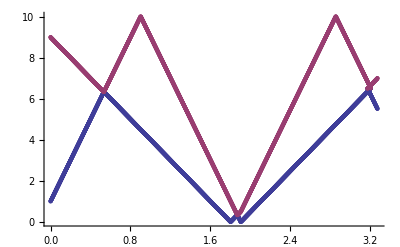

```mathematica
ListPlot[{V1,V2}]
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5},AnimationRunning->False]
```

```mathematica
Animate[Show[ListPlot[V1,Joined->True]],5]
```

Animate::vsform: Animate argument 5 does not have the correct form for a variable specification.

Animate[Show[ListPlot[V1,Joined→True]],5]

```mathematica
Animate[ListPointPlot3D[V1[[i]],Filling->Axis,PlotStyle->Red,PlotRange->{Full,{1,Length[data]},Automatic},AxesLabel->{x,"time","u(x,t)"}],{i,1,Length[data],1}]
```

```mathematica
V1[1]
```

{{0.,1.},{0.001,1.01},{0.002,1.02},{0.003,1.03},{0.004,1.04},{0.005,1.05},«3295»,{3.267,5.56},{3.268,5.55},{3.269,5.54},{3.27,5.53},{3.271,5.52},{3.272,5.51}}[1]

```mathematica
V1[[1]]
```

{0.,1.}

```mathematica
{0.,1.}
```

{0.,1.}

```mathematica
Graphics[V[[1]]]
```

Part::partd: Part specification V ⟦ 1 ⟧ is longer than depth of object.

-Graphics-

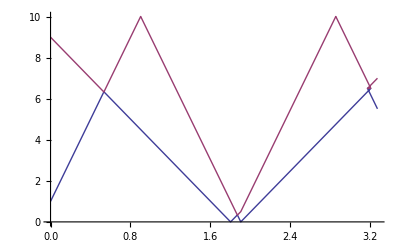

```mathematica
ListLinePlot[{V1,V2}]
```

```mathematica
Animate[Overlay[Table[SetAlphaChannel[imgs[[n]],(1+Tanh[tr (x-dt n)])/2],{n,1,Length[imgs],1}]],{x,0,dt (Length[imgs]+1),ImageSize->Small},AnimationRate->2]
```

Animate::vsform: Animate argument {x, 0, dt\ (Length[imgs] + 1), ImageSize → Small} does not have the correct form for a variable specification.

Animate[Overlay[Table[SetAlphaChannel[imgs⟦n⟧,1/2 (1+Tanh[tr (x-dt n)])],{n,1,Length[imgs],1}]],{x,0,dt (Length[imgs]+1),ImageSize→Small},AnimationRate→2]

```mathematica
Animator[V1]
```

Animator[{{0.,1.},{0.001,1.01},{0.002,1.02},{0.003,1.03},{0.004,1.04},{0.005,1.05},«3295»,{3.267,5.56},{3.268,5.55},{3.269,5.54},{3.27,5.53},{3.271,5.52},{3.272,5.51}}]

```mathematica
{sol, {steps}} = Reap[FindMinimum[(x-1)^2+100(y-x^2)^2,{{x,-1},{y,1}},StepMonitor:> Sow[{x,y}]]]
```

{{0.,{x→1.,y→1.}},{{{-0.798884,0.602235},{-0.693066,0.472618},{-0.501627,0.218389},{-0.401079,0.152716},{-0.203027,0.00395482},{0.00719502,-0.0435943},{0.217584,0.00265073},{0.418964,0.134094},{0.606503,0.331827},{0.779368,0.576986},{0.938738,0.855671},{1.,0.996247},{1.,1.}}}}

```mathematica
List[V1]
```

{{{0.,1.},{0.001,1.01},{0.002,1.02},{0.003,1.03},{0.004,1.04},{0.005,1.05},«3295»,{3.267,5.56},{3.268,5.55},{3.269,5.54},{3.27,5.53},{3.271,5.52},{3.272,5.51}}}

```mathematica
V1[1]
```

{{0.,1.},{0.001,1.01},{0.002,1.02},{0.003,1.03},{0.004,1.04},{0.005,1.05},«3295»,{3.267,5.56},{3.268,5.55},{3.269,5.54},{3.27,5.53},{3.271,5.52},{3.272,5.51}}[1]

```mathematica
V1[[1]]
```

{0.,1.}

```mathematica
V1[[3]]
```

{0.002,1.02}

```mathematica
list={{1,1},{2,1}}
```

{{1,1},{2,1}}

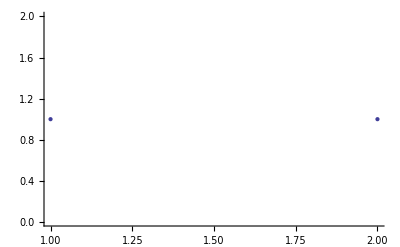

```mathematica
ListPlot[list]
```

```mathematica
list[[1]]
```

{1,1}

```mathematica
A={V1[[1050]]}
```

{{1.049,3.765}}

```mathematica
B={V2[[1050]]}
```

{{1.049,8.54}}

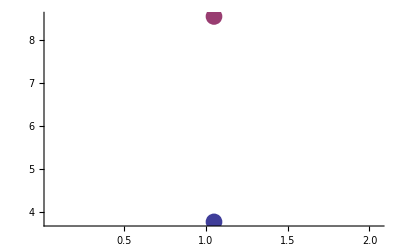

```mathematica
ListPlot[{A,B},PlotStyle->PointSize[0.03]]
```

```mathematica
A=Animate[ListPlot[{{V1[[n]]},{V2[[n]]}},PlotStyle->PointSize[0.03],PlotRange->{{0,4},{0,10}}],{n,1,3307,1},AnimationRunning->False]
```

```mathematica
Export["varios1.avi",A]
```

varios1.avi

```mathematica
B=Animate[ListPlot[{{R1[[n]]},{R2[[n]]}},PlotStyle->PointSize[0.03],PlotRange->{{0,1.2},{0,10}}],{n,1,1104,1},AnimationRunning->False]
```

```mathematica
Export["reposo.avi",B]
```

reposo.avi

```mathematica
H=Animate[ListPlot[{{I1[[n]]},{I2[[n]]}},PlotStyle->PointSize[0.03],PlotRange->{{0,3},{0,10}}],{n,1,2904,1},AnimationRunning->False]
```

```mathematica
Export["iguales.avi",H]
```

iguales.avi